# Population annealing analysis - fixed

## All trials: N = 256, R = 12, M = 10, K = 10, β = 10, J = 3, C = 4, S = 5, L = 6

N = number of spins
R = initial population size
M = number of MC sweeps per temperature step
K = number of temperature steps
β = target beta
J = J_{ij} matrix seed
C = MC sweep seed
S = initial spin seed
L = randfrom seed

## Import Relevant Files

```mathematica
SetDirectory[NotebookDirectory[]];
Clear["Global`*"];
trials=4;
steps=Range[1,10];
energies=Range[1,trials];
For[i=5,i≤4+trials,i++,
Evaluate[Symbol["energies"<>ToString[i-4]]]=Import["energies_t"<>ToString[i]<>".csv","CSV"];
energies⟦i-4⟧=Evaluate[Symbol["energies"<>ToString[i-4]]];
]
```

## Create Histograms

```mathematica
trial5=Manipulate[Histogram[energies⟦1⟧⟦sweeps+1⟧,50,Frame->True,FrameLabel->{"energy","replica frequency"},PlotLabel->"Trial 5: 1 Thread",LabelStyle->Black,FrameStyle->Black],{sweeps,0,Length[energies⟦1⟧]-1,1}];
trial6=Manipulate[Histogram[energies⟦2⟧⟦sweeps+1⟧,50,Frame->True,FrameLabel->{"energy","replica frequency"},PlotLabel->"Trial 6: 2 Threads",LabelStyle->Black,FrameStyle->Black],{sweeps,0,Length[energies⟦2⟧]-1,1}];
trial7=Manipulate[Histogram[energies⟦3⟧⟦sweeps+1⟧,50,Frame->True,FrameLabel->{"energy","replica frequency"},PlotLabel->"Trial 7: 3 Threads",LabelStyle->Black,FrameStyle->Black],{sweeps,0,Length[energies⟦3⟧]-1,1}];
trial8=Manipulate[Histogram[energies⟦4⟧⟦sweeps+1⟧,50,Frame->True,FrameLabel->{"energy","replica frequency"},PlotLabel->"Trial 8: 4 Threads",LabelStyle->Black,FrameStyle->Black],{sweeps,0,Length[energies⟦4⟧]-1,1}];
```

## Display Histograms

```mathematica
Grid[{{trial5,trial6},{trial7,trial8}}]
```

| 
 |

## Analyze Runtimes

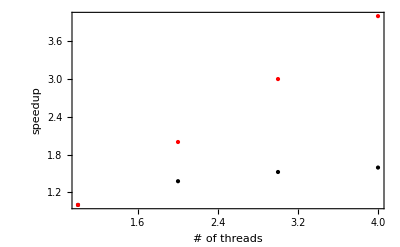

1.59391

```mathematica
threads={1,2,3,4};
times={110.144175,79.995294,72.302793,69.103095};
speedup=110.144175/times;
speedupPlot=ListPlot[Transpose[{threads,speedup}],PlotStyle->{Black,PointSize[Large]}];
idealPlot=ListPlot[Transpose[{threads,threads}],PlotStyle->{Red,PointSize[Large]}];
Show[speedupPlot,idealPlot,Frame->True,PlotRange->All,FrameLabel->{"# of threads","speedup"}]
speedup[[4]]
```